# Decision boundary

```mathematica
f[fbase_, steps_, L_, r_, delta_] = (L - 1 - r * Sum[((delta/(1+r))^t)*(fbase * L - fbase * t),{t, 1,steps}])/(L - 1 - r * Sum[((delta/(1+r))^t)*(L - t),{t, 1,steps}])
```

(-1+L-(delta fbase r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)/(-1+L-(delta r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)

30

{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,0.988806,0.978755,0.969844,0.962036,0.955265,0.949451,0.9445,0.940318,0.93681,0.933887,0.931466,0.929473,0.927841,0.926512,0.925436,0.924571,0.923878,0.923329,0.922895,0.922557,0.922295,0.922096,0.921946,0.921836,0.921757,0.921703,0.921668,0.921648,0.92164,0.92164},{1.,0.977612,0.957509,0.939688,0.924071,0.91053,0.898902,0.889,0.880636,0.87362,0.867774,0.862932,0.858946,0.855682,0.853024,0.850873,0.849141,0.847757,0.846657,0.84579,0.845113,0.84459,0.844191,0.843891,0.843671,0.843514,0.843406,0.843336,0.843296,0.843279,0.843279},{1.,0.966418,0.936264,0.909532,0.886107,0.865796,0.848352,0.8335,0.820954,0.81043,0.801661,0.794398,0.788418,0.783522,0.779536,0.776309,0.773712,0.771635,0.769986,0.768686,0.76767,0.766885,0.766287,0.765837,0.765507,0.76527,0.765108,0.765004,0.764945,0.764919,0.764919},{1.,0.955224,0.915019,0.879375,0.848142,0.821061,0.797803,0.778001,0.761272,0.74724,0.735547,0.725864,0.717891,0.711363,0.706048,0.701746,0.698283,0.695514,0.693314,0.691581,0.690227,0.689181,0.688382,0.687783,0.687342,0.687027,0.686811,0.686672,0.686593,0.686559,0.686559}}

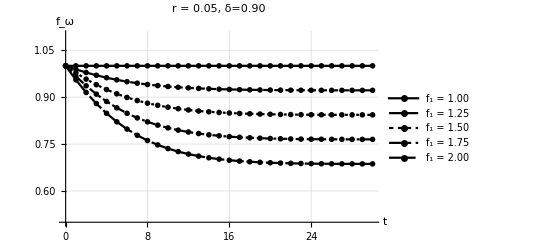

```mathematica
layers = 30
data = Table[Table[f[factor,x,layers,0.05,0.9], {x,0,layers,1}], {factor, 1., 2., 0.25}]
ListLinePlot[data, PlotTheme->"Monochrome", PlotRange -> {0.5, 1.1}, AxesLabel->{"t", "f_ω"},PlotLabel-> "r = 0.05, δ=0.90", PlotLegends->{"f_1 = 1.00","f_1 = 1.25", "f_1 = 1.50", "f_1 = 1.75", "f_1 = 2.00"}, GridLines->Automatic, DataRange->{0, layers}]
```